```mathematica
Exit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/viktor/Documents/KerrSpinningFluxes

```mathematica
Get["/home/viktor/Documents/KerrSpinningFluxes/SpinningTrajectory.wl"]
```

```mathematica
Get["/home/viktor/Documents/KerrSpinningFluxes/TeukolskySpinFluxes.wl"]
```

## Fluxes

```mathematica
a=0.9`64
p=12.0`64
e=0.2`64
x=0.8`64
```

0.9

12.

0.2

0.8

```mathematica
corr=KerrSpinOrbitCorrection[a,p,e,x,12,12]
```

Calculating t, ϕ equations

Calculating r equation

Calculating θ equation

Calculating norm equation

Calculating submatrices

Calculating v

Calculating ES,LS

Calculating UtSlist, UϕSlist

Calculating Uthatlist, Uϕhatlist

Calculating UtSfour, UϕSfour

Calculating Uthatfour, Uϕhatfour

Calculating ImΔtSfour, ImΔϕSfour

<|a→0.9,p→12.,e→0.2,ℐ→0.643501108793284386802809228717322638041510591115312382865606119,Ehat→0.96181291429748625538439133098094481922633837037195159298579579,Lzhat→3.03161436070341245886292657730611059741395637677064636256094,Khat→9.88308737027204536842554533587846408566536767270694660904733,TrajectoryCorrection→{Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`ΔtS$7037[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`rS$7037[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`zS$7037[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`ΔϕS$7037[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]]},TrajectoryGeo→{Function[{qt$,qr$,qθ$},qt$+48.7546583889972715911545467824241863094333535778542944584424 (0.999621186185168170879221408184941614969109434390677695667233 (π/2+qθ$)-EllipticE[JacobiAmplitude[1.00037902921429652149974839053380540449676976347382220058765 (π/2+qθ$),0.00151482473241564322777341551704172778511678764551789095703798],0.00151482473241564322777341551704172778511678764551789095703798])-0.305733809672158824411196025507280483258888727395579562915329 (-39.2943237760882513369442197338687920179576619927359622632983 (52.96673554130676524177597872983127962060565512450012191 (0.5057057521902615098173498845441398074976264454311385121 qr$-EllipticPi[4.768530103923284761684651497273243069669553326495134332×10^-6,JacobiAmplitude[0.50570453959371911018167899261150577447815643645023296095306 qr$,0.044487446019535530635905997035572609594821072843087793459219],0.044487446019535530635905997035572609594821072843087793459219])+0.11715195845777098409257832828241292225366987588396038702443 (0.51459418827437318612569577829177488261730218860161383541106 qr$-EllipticPi[0.034061311284131832840296579847330817961066277269234984937865,JacobiAmplitude[0.50570453959371911018167899261150577447815643645023296095306 qr$,0.044487446019535530635905997035572609594821072843087793459219],0.044487446019535530635905997035572609594821072843087793459219]))+262.885627960254677715898167333130445488260289373965599623574 (0.6372621437871158790716000572101107298327994468226104555409 qr$-EllipticPi[0.368622843612544278882703912066410849893514926725741964886075,JacobiAmplitude[0.50570453959371911018167899261150577447815643645023296095306 qr$,0.044487446019535530635905997035572609594821072843087793459219],0.044487446019535530635905997035572609594821072843087793459219])+132.105277352181554864585837589416944708426914791148306365859 (0.49439180196787301068872607087578024595411969557652655741129 qr$-EllipticE[JacobiAmplitude[0.50570453959371911018167899261150577447815643645023296095306 qr$,0.044487446019535530635905997035572609594821072843087793459219],0.044487446019535530635905997035572609594821072843087793459219]+(0.368622843612544278882703912066410849893514926725741964886075 JacobiCN[0.50570453959371911018167899261150577447815643645023296095306 qr$,0.044487446019535530635905997035572609594821072843087793459219] JacobiSN[0.50570453959371911018167899261150577447815643645023296095306 qr$,0.044487446019535530635905997035572609594821072843087793459219] √(1-0.044487446019535530635905997035572609594821072843087793459219 JacobiSN[0.50570453959371911018167899261150577447815643645023296095306 qr$,0.044487446019535530635905997035572609594821072843087793459219]^2))/(1-0.368622843612544278882703912066410849893514926725741964886075 JacobiSN[0.50570453959371911018167899261150577447815643645023296095306 qr$,0.044487446019535530635905997035572609594821072843087793459219]^2))),Listable],Function[{qr$},(-135.639993197368124523046115283307128377549106962975024879818+7.1800034013159377384769423583464358112254465185124875600908 JacobiSN[0.50570453959371911018167899261150577447815643645023296095306 qr$,0.044487446019535530635905997035572609594821072843087793459219]^2)/(-13.5639993197368124523046115283307128377549106962975024879818+5. JacobiSN[0.50570453959371911018167899261150577447815643645023296095306 qr$,0.044487446019535530635905997035572609594821072843087793459219]^2),Listable],Function[{qθ$},ArcCos[0.6 JacobiSN[1.00037902921429652149974839053380540449676976347382220058765 (π/2+qθ$),0.00151482473241564322777341551704172778511678764551789095703798]],Listable],Function[{qϕ$,qr$,qθ$},qϕ$+0.631261316834828744764015148589993765497076646706724285810542 (315.9065948775168213973206983141006382982593414594791075 (0.5057057521902615098173498845441398074976264454311385121 qr$-EllipticPi[4.768530103923284761684651497273243069669553326495134332×10^-6,JacobiAmplitude[0.50570453959371911018167899261150577447815643645023296095306 qr$,0.044487446019535530635905997035572609594821072843087793459219],0.044487446019535530635905997035572609594821072843087793459219])+1.7785345139126208658021563405976115777297702978989644058556 (0.51459418827437318612569577829177488261730218860161383541106 qr$-EllipticPi[0.034061311284131832840296579847330817961066277269234984937865,JacobiAmplitude[0.50570453959371911018167899261150577447815643645023296095306 qr$,0.044487446019535530635905997035572609594821072843087793459219],0.044487446019535530635905997035572609594821072843087793459219]))-0.798315087076201573729368925868590051780254792302667919699966 (1.25052644609046222195210361926814317068583723418386042333939 (π/2+qθ$)-EllipticPi[0.36,JacobiAmplitude[1.00037902921429652149974839053380540449676976347382220058765 (π/2+qθ$),0.00151482473241564322777341551704172778511678764551789095703798],0.00151482473241564322777341551704172778511678764551789095703798]),Listable]},MinoFrequenciesGeo→{174.488290417693788710739301034869303845292037964131774,3.110428970017385652526063796200874731199659497288760018505,3.7960772315595681291670711482126580725255727130391319895241,3.9417327935526137349256963307982787222088793703826859},BLFrequenciesGeo→{0.0178260040405667021394318819955008665557841120966108165,0.0217554841214412585580725346294331000558248472550501807,0.022590242497744746986450141392703389503048511537721411},FourVelocityCorrection→{Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`udtS$7037[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},(12. 0.2 (SpinningOrbit`Private`χrhat$7037'[SpinningOrbit`Private`wr$] (Cos[SpinningOrbit`Private`χrhat$7037[SpinningOrbit`Private`wr$]] SpinningOrbit`Private`δχrS$7037[SpinningOrbit`Private`wr$] SpinningOrbit`Private`Υrhat$7037+Sin[SpinningOrbit`Private`χrhat$7037[SpinningOrbit`Private`wr$]] SpinningOrbit`Private`ΥrS$7037+(2 0.2 Sin[SpinningOrbit`Private`χrhat$7037[SpinningOrbit`Private`wr$]]^2 SpinningOrbit`Private`δχrS$7037[SpinningOrbit`Private`wr$] SpinningOrbit`Private`Υrhat$7037)/(1+0.2 Cos[SpinningOrbit`Private`χrhat$7037[SpinningOrbit`Private`wr$]]))+Sin[SpinningOrbit`Private`χrhat$7037[SpinningOrbit`Private`wr$]] SpinningOrbit`Private`dδχrS$7037[SpinningOrbit`Private`wr$]))/(1+0.2 Cos[SpinningOrbit`Private`χrhat$7037[SpinningOrbit`Private`wr$]])^2+SpinningOrbit`Private`dδ𝔯$7037[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},-Sin[SpinningOrbit`Private`ℐ$7037] (SpinningOrbit`Private`χθhat$7037'[SpinningOrbit`Private`wz$] (Cos[SpinningOrbit`Private`χθhat$7037[SpinningOrbit`Private`wz$]] SpinningOrbit`Private`δχθS$7037[SpinningOrbit`Private`wz$] SpinningOrbit`Private`Υθhat$7037+Sin[SpinningOrbit`Private`χθhat$7037[SpinningOrbit`Private`wz$]] SpinningOrbit`Private`ΥθS$7037)+Sin[SpinningOrbit`Private`χθhat$7037[SpinningOrbit`Private`wz$]] SpinningOrbit`Private`dδχθS$7037[SpinningOrbit`Private`wz$])+SpinningOrbit`Private`dδ𝔷$7037[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`udϕS$7037[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]]},Spin4vector→{Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`St$7037[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`Sr$7037[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`Sz$7037[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`Sϕ$7037[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]]},TrajectoryDeltas→<|Δtr→Function[{qr$},-0.305733809672158824411196025507280483258888727395579562915329 (-39.2943237760882513369442197338687920179576619927359622632983 (52.96673554130676524177597872983127962060565512450012191 (0.5057057521902615098173498845441398074976264454311385121 qr$-EllipticPi[4.768530103923284761684651497273243069669553326495134332×10^-6,JacobiAmplitude[0.50570453959371911018167899261150577447815643645023296095306 qr$,0.044487446019535530635905997035572609594821072843087793459219],0.044487446019535530635905997035572609594821072843087793459219])+0.11715195845777098409257832828241292225366987588396038702443 (0.51459418827437318612569577829177488261730218860161383541106 qr$-EllipticPi[0.034061311284131832840296579847330817961066277269234984937865,JacobiAmplitude[0.50570453959371911018167899261150577447815643645023296095306 qr$,0.044487446019535530635905997035572609594821072843087793459219],0.044487446019535530635905997035572609594821072843087793459219]))+262.885627960254677715898167333130445488260289373965599623574 (0.6372621437871158790716000572101107298327994468226104555409 qr$-EllipticPi[0.368622843612544278882703912066410849893514926725741964886075,JacobiAmplitude[0.50570453959371911018167899261150577447815643645023296095306 qr$,0.044487446019535530635905997035572609594821072843087793459219],0.044487446019535530635905997035572609594821072843087793459219])+132.105277352181554864585837589416944708426914791148306365859 (0.49439180196787301068872607087578024595411969557652655741129 qr$-EllipticE[JacobiAmplitude[0.50570453959371911018167899261150577447815643645023296095306 qr$,0.044487446019535530635905997035572609594821072843087793459219],0.044487446019535530635905997035572609594821072843087793459219]+(0.368622843612544278882703912066410849893514926725741964886075 JacobiCN[0.50570453959371911018167899261150577447815643645023296095306 qr$,0.044487446019535530635905997035572609594821072843087793459219] JacobiSN[0.50570453959371911018167899261150577447815643645023296095306 qr$,0.044487446019535530635905997035572609594821072843087793459219] √(1-0.044487446019535530635905997035572609594821072843087793459219 JacobiSN[0.50570453959371911018167899261150577447815643645023296095306 qr$,0.044487446019535530635905997035572609594821072843087793459219]^2))/(1-0.368622843612544278882703912066410849893514926725741964886075 JacobiSN[0.50570453959371911018167899261150577447815643645023296095306 qr$,0.044487446019535530635905997035572609594821072843087793459219]^2))),Listable],Δtθ→Function[{qθ$},48.7546583889972715911545467824241863094333535778542944584424 (0.999621186185168170879221408184941614969109434390677695667233 (π/2+qθ$)-EllipticE[JacobiAmplitude[1.00037902921429652149974839053380540449676976347382220058765 (π/2+qθ$),0.00151482473241564322777341551704172778511678764551789095703798],0.00151482473241564322777341551704172778511678764551789095703798]),Listable],Δϕr→Function[{qr$},0.631261316834828744764015148589993765497076646706724285810542 (315.9065948775168213973206983141006382982593414594791075 (0.5057057521902615098173498845441398074976264454311385121 qr$-EllipticPi[4.768530103923284761684651497273243069669553326495134332×10^-6,JacobiAmplitude[0.50570453959371911018167899261150577447815643645023296095306 qr$,0.044487446019535530635905997035572609594821072843087793459219],0.044487446019535530635905997035572609594821072843087793459219])+1.7785345139126208658021563405976115777297702978989644058556 (0.51459418827437318612569577829177488261730218860161383541106 qr$-EllipticPi[0.034061311284131832840296579847330817961066277269234984937865,JacobiAmplitude[0.50570453959371911018167899261150577447815643645023296095306 qr$,0.044487446019535530635905997035572609594821072843087793459219],0.044487446019535530635905997035572609594821072843087793459219])),Listable],Δϕθ→Function[{qθ$},-0.798315087076201573729368925868590051780254792302667919699966 (1.25052644609046222195210361926814317068583723418386042333939 (π/2+qθ$)-EllipticPi[0.36,JacobiAmplitude[1.00037902921429652149974839053380540449676976347382220058765 (π/2+qθ$),0.00151482473241564322777341551704172778511678764551789095703798],0.00151482473241564322777341551704172778511678764551789095703798]),Listable]|>,MinoFrequenciesCorrection→{-0.2470440007319329864,0.1305961472134457436,-0.0640537142915908316,-0.13108665000317915769},BLFrequenciesCorrection→{0.00077369062557450230986,-0.00033629278111386463239,-0.00071927959073123556524},ES→-0.00094346847435512159302,LS→0.553855167650680016001,δχrS→SpinningOrbit`Private`δχrS$7037,δχθS→SpinningOrbit`Private`δχθS$7037,δr→SpinningOrbit`Private`δ𝔯$7037,δz→SpinningOrbit`Private`δ𝔷$7037,OrbitCorrection→Function[{SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$},SpinningOrbit`Private`OrbitCorrection$7037[SpinningOrbit`Private`wr$,SpinningOrbit`Private`wz$]],error→0.|>

```mathematica
corr["error"]
```

0.

```mathematica
l=2
m=2
n=1
k=1
```

2

2

1

1

```mathematica
PacletDirectoryLoad["~/BHPT/SpinWeightedSpheroidalHarmonics-master"]
```

{/home/viktor/BHPT/SpinWeightedSpheroidalHarmonics-master}

```mathematica
<<Teukolsky`
```

```mathematica
modes0=Table[TeukolskySpinModeFromCorrection[l,m,n,k,corr,s*0.01`64],{s,{-1,-1/2,1/2,1}}]
```

64 steps in wr, 32 steps in wθ

64 steps in wr, 32 steps in wθ

64 steps in wr, 32 steps in wθ

«1 more identical outputs»

{<|l→2,m→2,k→1,n→1,ω→0.084771984770867473004935,Amplitudes→<|ℐ→-9.888302698629168×10^-7-2.6948771162054885×10^-6 ⅈ,ℋ→8.73700977909286197×10^-6-0.00003009962330682453319 ⅈ|>,α→-0.0042914754873947964068261,S→0.1523572106878393612331,Fluxes→<|Energy→<|ℐ→9.124738850027341×10^-11,ℋ→-4.66816537540605259×10^-11|>,AngularMomentum→<|ℐ→2.152772257176908×10^-9,ℋ→-1.101346249712983612×10^-9|>|>,stepsr→64,stepsθ→32|>,<|l→2,m→2,k→1,n→1,ω→0.0847669789641824638376697,Amplitudes→<|ℐ→-9.8936687164860915×10^-7-2.696430601039804×10^-6 ⅈ,ℋ→8.716050539426073149×10^-6-0.0000300275490853406111 ⅈ|>,α→-0.0042908378037831286087949,S→0.15235752530744997469287,Fluxes→<|Energy→<|ℐ→9.1362676898970241×10^-11,ℋ→-4.645691221455115069×10^-11|>,AngularMomentum→<|ℐ→2.1556195116396617×10^-9,ℋ→-1.09610871549830996×10^-9|>|>,stepsr→64,stepsθ→32|>,<|l→2,m→2,k→1,n→1,ω→0.0847569673508124455031397,Amplitudes→<|ℐ→-9.9043087843181934×10^-7-2.6995394904410147×10^-6 ⅈ,ℋ→8.674121576165473109×10^-6-0.0000298833879080674653 ⅈ|>,α→-0.0042895625822907569264127,S→0.15235815454693145321939,Fluxes→<|Energy→<|ℐ→9.1593426048021434×10^-11,ℋ→-4.600903107374865707×10^-11|>,AngularMomentum→<|ℐ→2.1613190964917991×10^-9,ℋ→-1.085669591818108706×10^-9|>|>,stepsr→64,stepsθ→32|>,<|l→2,m→2,k→1,n→1,ω→0.084751961544127436335875,Amplitudes→<|ℐ→-9.909582874880308×10^-7-2.7010948939316444×10^-6 ⅈ,ℋ→8.65315185307224704×10^-6-0.00002981130095484222985 ⅈ|>,α→-0.0042889250444125016062619,S→0.1523584691668023136972,Fluxes→<|Energy→<|ℐ→9.170888677439357×10^-11,ℋ→-4.578589160490224562×10^-11|>,AngularMomentum→<|ℐ→2.164171426914854×10^-9,ℋ→-1.080468009724190371×10^-9|>|>,stepsr→64,stepsθ→32|>}

```mathematica
modesNew=Table[TeukolskySpinModeFromCorrectionNew[l,m,n,k,corr,s*0.01`64],{s,{-1,-1/2,1/2,1}}]
```

64 steps in wr, 32 steps in wθ

64 steps in wr, 32 steps in wθ

64 steps in wr, 32 steps in wθ

«1 more identical outputs»

{<|l→2,m→2,k→1,n→1,ω→0.084771984770867473004935,Amplitudes→<|ℐ→-9.8883200079917668×10^-7-2.6948850193546686×10^-6 ⅈ,ℋ→8.737009184453687767×10^-6-0.00003009962329759956913 ⅈ|>,α→-0.0042914754873947964068261,S→0.1523572106878393612331,Fluxes→<|Energy→<|ℐ→9.1247898095622798×10^-11,ℋ→-4.668165323388445077×10^-11|>,AngularMomentum→<|ℐ→2.1527842799070766×10^-9,ℋ→-1.101346237440625556×10^-9|>|>,stepsr→64,stepsθ→32|>,<|l→2,m→2,k→1,n→1,ω→0.0847669789641824638376697,Amplitudes→<|ℐ→-9.8936730440734913×10^-7-2.69643257629341196×10^-6 ⅈ,ℋ→8.716050390740802308×10^-6-0.00003002754908302928378 ⅈ|>,α→-0.0042908378037831286087949,S→0.15235752530744997469287,Fluxes→<|Energy→<|ℐ→9.1362804354513533×10^-11,ℋ→-4.645691208478739935×10^-11|>,AngularMomentum→<|ℐ→2.1556225188376261×10^-9,ℋ→-1.09610871243665192×10^-9|>|>,stepsr→64,stepsθ→32|>,<|l→2,m→2,k→1,n→1,ω→0.0847569673508124455031397,Amplitudes→<|ℐ→-9.9043131123974401×10^-7-2.69954146462752271×10^-6 ⅈ,ℋ→8.67412142742925978×10^-6-0.0000298833879057459495 ⅈ|>,α→-0.0042895625822907569264127,S→0.15235815454693145321939,Fluxes→<|Energy→<|ℐ→9.1593553617186152×10^-11,ℋ→-4.60090309445460269×10^-11|>,AngularMomentum→<|ℐ→2.1613221067260891×10^-9,ℋ→-1.085669588769329728×10^-9|>|>,stepsr→64,stepsθ→32|>,<|l→2,m→2,k→1,n→1,ω→0.084751961544127436335875,Amplitudes→<|ℐ→-9.9096001881776848×10^-7-2.7011027885440253×10^-6 ⅈ,ℋ→8.65315125802553293×10^-6-0.00002981130094553575802 ⅈ|>,α→-0.0042889250444125016062619,S→0.1523584691668023136972,Fluxes→<|Energy→<|ℐ→9.1709397278713267×10^-11,ℋ→-4.578589108921514064×10^-11|>,AngularMomentum→<|ℐ→2.1641834739356052×10^-9,ℋ→-1.080467997554864834×10^-9|>|>,stepsr→64,stepsθ→32|>}

```mathematica
Table[modes0[[i]]["Amplitudes"]["ℐ"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/(0.005`64)
```

-1.064006106761×10^-7-3.1088895805882×10^-7 ⅈ

```mathematica
Table[modesNew[[i]]["Amplitudes"]["ℐ"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/(0.005`64)
```

-1.0640061067612×10^-7-3.1088895805882×10^-7 ⅈ

```mathematica
1-%/%%
```

0.+0. ⅈ

```mathematica
%/0.005`48^4
```

0.+0. ⅈ

```mathematica
Table[modes0[[i]]["Amplitudes"]["ℋ"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/(0.005`64)
```

-4.19289633440309×10^-6+0.00001441611777004772 ⅈ

```mathematica
Table[modesNew[[i]]["Amplitudes"]["ℋ"],{i,1,4}].{1/12,-2/3,2/3,-1/12}/(0.005`64)
```

-4.19289633440309×10^-6+0.000014416117770047719 ⅈ

```mathematica
1-%/%%
```

0.+0. ⅈ

```mathematica
%/0.005`48^4
```

0.+0. ⅈ

```mathematica
listspar={8,4,2,1,1/2,1/4,1/8,1/16}*0.01`64
```

{0.08,0.04,0.02,0.01,0.005,0.0025,0.00125,0.000625}

```mathematica
modesOldpex=Table[TeukolskySpinModeFromCorrectionNew[l,m,n,k,corr,listspar[[i]]],{i,1,Length[listspar]}]
```

64 steps in wr, 32 steps in wθ

64 steps in wr, 32 steps in wθ

64 steps in wr, 32 steps in wθ

«5 more identical outputs»

{<|l→2,m→2,k→1,n→1,ω→0.084681880250537307994164,Amplitudes→<|ℐ→-9.981325599733402×10^-7-2.723440648907061×10^-6 ⅈ,ℋ→8.35917080242762137×10^-6-0.0000288016382396464941 ⅈ|>,α→-0.004280004615599615356361,S→0.1523628738541014801889,Fluxes→<|Energy→<|ℐ→9.336423932394007×10^-11,ℋ→-4.27180234308654562×10^-11|>,AngularMomentum→<|ℐ→2.205058249715651×10^-9,ℋ→-1.00890587938012653×10^-9|>|>,stepsr→64,stepsθ→32|>,<|l→2,m→2,k→1,n→1,ω→0.084721926704017381332284,Amplitudes→<|ℐ→-9.940862727752131×10^-7-2.710566804914117×10^-6 ⅈ,ℋ→8.52725061933637887×10^-6-0.000029378690061744165 ⅈ|>,α→-0.004285100837371074047403,S→0.1523603568878490290156,Fluxes→<|Energy→<|ℐ→9.241104642223244×10^-11,ℋ→-4.44582662364610082×10^-11|>,AngularMomentum→<|ℐ→2.181514278944047×10^-9,ℋ→-1.04951027357485407×10^-9|>|>,stepsr→64,stepsθ→32|>,<|l→2,m→2,k→1,n→1,ω→0.084741949930757418001345,Amplitudes→<|ℐ→-9.92010856444142×10^-7-2.7042391749792852×10^-6 ⅈ,ℋ→8.61119954421609247×10^-6-0.00002966711428838719209 ⅈ|>,α→-0.004287650114397970908939,S→0.1523590984068042656095,Fluxes→<|Energy→<|ℐ→9.19420242572666×10^-11,ℋ→-4.53412131477356598×10^-11|>,AngularMomentum→<|ℐ→2.169929399368137×10^-9,ℋ→-1.07010077499476777×10^-9|>|>,stepsr→64,stepsθ→32|>,<|l→2,m→2,k→1,n→1,ω→0.084751961544127436335875,Amplitudes→<|ℐ→-9.9096001881776848×10^-7-2.7011027885440253×10^-6 ⅈ,ℋ→8.65315125802553293×10^-6-0.00002981130094553575802 ⅈ|>,α→-0.0042889250444125016062619,S→0.1523584691668023136972,Fluxes→<|Energy→<|ℐ→9.1709397278713267×10^-11,ℋ→-4.578589108921514064×10^-11|>,AngularMomentum→<|ℐ→2.1641834739356052×10^-9,ℋ→-1.080467997554864834×10^-9|>|>,stepsr→64,stepsθ→32|>,<|l→2,m→2,k→1,n→1,ω→0.0847569673508124455031397,Amplitudes→<|ℐ→-9.9043131123974401×10^-7-2.69954146462752271×10^-6 ⅈ,ℋ→8.67412142742925978×10^-6-0.0000298833879057459495 ⅈ|>,α→-0.0042895625822907569264127,S→0.15235815454693145321939,Fluxes→<|Energy→<|ℐ→9.1593553617186152×10^-11,ℋ→-4.60090309445460269×10^-11|>,AngularMomentum→<|ℐ→2.1613221067260891×10^-9,ℋ→-1.085669588769329728×10^-9|>|>,stepsr→64,stepsθ→32|>,<|l→2,m→2,k→1,n→1,ω→0.0847594702541549500867722,Amplitudes→<|ℐ→-9.9016613365159064×10^-7-2.69876252295883504×10^-6 ⅈ,ℋ→8.684605090239520417×10^-6-0.000029919429793160930806 ⅈ|>,α→-0.0042898813694470967304315,S→0.15235799723702855285391,Fluxes→<|Energy→<|ℐ→9.1535749163345507×10^-11,ℋ→-4.612080106356534819×10^-11|>,AngularMomentum→<|ℐ→2.159894319510766×10^-9,ℋ→-1.088274877728001947×10^-9|>|>,stepsr→64,stepsθ→32|>,<|l→2,m→2,k→1,n→1,ω→0.0847607217058262023785884,Amplitudes→<|ℐ→-9.90033339278208675×10^-7-2.69837348110844526×10^-6 ⅈ,ℋ→8.689846566137114392×10^-6-0.000029937450338672784517 ⅈ|>,α→-0.0042900407675795027326542,S→0.15235791858208523526501,Fluxes→<|Energy→<|ℐ→9.15068761960275198×10^-11,ℋ→-4.6176736167307009697×10^-11|>,AngularMomentum→<|ℐ→2.15918114792874886×10^-9,ℋ→-1.0895786453440015212×10^-9|>|>,stepsr→64,stepsθ→32|>,<|l→2,m→2,k→1,n→1,ω→0.08476134743166182852449657,Amplitudes→<|ℐ→-9.89966890226309081×10^-7-2.69817906824571884×10^-6 ⅈ,ℋ→8.6924672152227943439×10^-6-0.000029946460511838849392 ⅈ|>,α→-0.00429012046778425639077503,S→0.152357879254615609634701,Fluxes→<|Energy→<|ℐ→9.14924470623094624×10^-11,ℋ→-4.6204716229691554213×10^-11|>,AngularMomentum→<|ℐ→2.15882474346162395×10^-9,ℋ→-1.0902308099088147279×10^-9|>|>,stepsr→64,stepsθ→32|>}

```mathematica
r1=p/(1-e)
r2=p/(1+e)
z1=Sqrt[1-x^2]
```

15.

10.

0.6

```mathematica
r1S=14.82194059906608056193273398763418391241032712357072524225634175563136817989492`59.26267647183203;r2S=-14.21141889319576563189809355464959997292452893838422882050597695470562236382046`59.29889914959862;
z1S=0.00675302307993867879497385742600893565562838762604497938784410322208171244797`56.87055034254505;
```

```mathematica
orbitspex=Table[KerrSpinOrbit[a,2*(r1-spar*r1S)*(r2-spar*r2S)/((r1-spar*r1S)+(r2-spar*r2S)),((r1-spar*r1S)-(r2-spar*r2S))/((r1-spar*r1S)+(r2-spar*r2S)),Sqrt[1-(z1-spar*z1S)^2],spar],{spar,listspar}]
```

{<|a→0.9,p→12.331936450004959396072348131101558469429657356588576516583,e→0.10730288399205692450607917555202796017932507994926338941766,x→0.800404896508274439968759629033222877463838352944708471911012,spar→0.08,Energy→0.961738338610479886763273837328705725808575147638050009501,AngularMomentum→3.0652778515615793674074871303906024743954736232069988982,CarterConstantK→10.130946816350859966669461084766194426702696568957254803,EnTilde→0.962681616983302390646988547816102900024192214895802639021,JzTilde→3.0508508839601155224579898540930556132117276690191612161,KTilde→10.035333980287172781961926300734680939667693478175478494,Frequencies→<|Υ_r→3.0820316857904238624470036259283656246593063961918,Υ_z→3.77458856106630219830902364088320710559395600235454,Υ_ϕ→3.9237427527869299749953206265825941954659199,Υ_t→172.3290591631677204437814313615221569671517239|>,BLFrequencies→{0.0178845732736940135573337862271920660116356409,0.02190337821952812905576561413866478082652779009,0.0227688978970852548327946875785102360301966554},TrajectoryDeltas→<|Δtr→Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`orbitTilde$58310[TrajectoryDeltas][Δtr][SpinningOrbit`Private`qr$]-(3 0.08 SpinningOrbit`Private`τTilde$58310[ProperTime][0,SpinningOrbit`Private`qr$,0])/(2 SpinningOrbit`Private`sqrtK$58310)],Δtz→Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`orbitTilde$58310[TrajectoryDeltas][Δtθ][SpinningOrbit`Private`qz$]-(3 0.08 SpinningOrbit`Private`τTilde$58310[ProperTime][0,0,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$58310)],Δϕr→Function[{qr$},0.634614519627452368951164099330012792959074672516479 (199.4573136025646780995869122355267565243359347 (0.5081196860526042989488593199964307577064806245 qr$-EllipticPi[0.00001665642104621032649993873298817016617594951717,JacobiAmplitude[0.50811542010436963354358254170751519499626186839207 qr$,0.06261710509426306015537748119056507800478583661241],0.06261710509426306015537748119056507800478583661241])+1.7422900455113756586259993343017401494561330629393 (0.52090422175131833825216968244489583794588423334685 qr$-EllipticPi[0.048120212207240886255183534331064054734431952632842,JacobiAmplitude[0.50811542010436963354358254170751519499626186839207 qr$,0.06261710509426306015537748119056507800478583661241],0.06261710509426306015537748119056507800478583661241])),Listable],Δϕz→Function[{qθ$},-0.798146280745641438105681090802529761218676015770911 (1.2508139097503131734946182556082775397254171478546 (π/2+qθ$)-EllipticPi[0.360299369574019045982410710824737266387982671157974705512,JacobiAmplitude[1.00037530832112566277407598444911265622548547309672 (π/2+qθ$),0.00149996639642152143838847280938137489066515084079116],0.00149996639642152143838847280938137489066515084079116]),Listable]|>,Trajectoryg→{Function[{SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},SpinningOrbit`Private`orbitTilde$58310[Trajectory]⟦1⟧[SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]-1/(2 SpinningOrbit`Private`sqrtK$58310)3 0.08 SpinningOrbit`Private`τTilde$58310[ProperTime][0,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]],Function[{qr$},(-137.771571148417511256858837810762875674127493472251+10.25071307898057730376056046101778998636074896561 JacobiSN[0.50811542010436963354358254170751519499626186839207 qr$,0.06261710509426306015537748119056507800478583661241]^2)/(-14.9295369464491572833387624064218021391905753601234+7.13757747340631023773721528634468485491360723498561 JacobiSN[0.50811542010436963354358254170751519499626186839207 qr$,0.06261710509426306015537748119056507800478583661241]^2),Listable],SpinningOrbit`Private`zTilde$58310,Function[{qϕ$,qr$,qθ$},qϕ$+0.634614519627452368951164099330012792959074672516479 (199.4573136025646780995869122355267565243359347 (0.5081196860526042989488593199964307577064806245 qr$-EllipticPi[0.00001665642104621032649993873298817016617594951717,JacobiAmplitude[0.50811542010436963354358254170751519499626186839207 qr$,0.06261710509426306015537748119056507800478583661241],0.06261710509426306015537748119056507800478583661241])+1.7422900455113756586259993343017401494561330629393 (0.52090422175131833825216968244489583794588423334685 qr$-EllipticPi[0.048120212207240886255183534331064054734431952632842,JacobiAmplitude[0.50811542010436963354358254170751519499626186839207 qr$,0.06261710509426306015537748119056507800478583661241],0.06261710509426306015537748119056507800478583661241]))-0.798146280745641438105681090802529761218676015770911 (1.2508139097503131734946182556082775397254171478546 (π/2+qθ$)-EllipticPi[0.360299369574019045982410710824737266387982671157974705512,JacobiAmplitude[1.00037530832112566277407598444911265622548547309672 (π/2+qθ$),0.00149996639642152143838847280938137489066515084079116],0.00149996639642152143838847280938137489066515084079116]),Listable]},δx→Function[{SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},{SpinningOrbit`Private`δt3[SpinningOrbit`Private`rTilde$58310[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58310[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$58310[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$58310[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$58310,0.9],SpinningOrbit`Private`δr3[SpinningOrbit`Private`rTilde$58310[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58310[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$58310,SpinningOrbit`Private`JzTilde$58310,SpinningOrbit`Private`KTilde$58310,0.9],SpinningOrbit`Private`δz3[SpinningOrbit`Private`rTilde$58310[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58310[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$58310,SpinningOrbit`Private`JzTilde$58310,SpinningOrbit`Private`KTilde$58310,0.9],SpinningOrbit`Private`δϕ3[SpinningOrbit`Private`rTilde$58310[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58310[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$58310[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$58310[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$58310,0.9]}],FourVelocitiesg→{Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`UrTilde$58310[SpinningOrbit`Private`qr$]],Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`UzTilde$58310[SpinningOrbit`Private`qz$]]},rootsTilde→{9.228120848127517910654433086475220279777742079493011714,16.36569832153382814839164837281990513469134931447862171}|>,<|a→0.9,p→12.1927943293996654385124882032210647873424925203971264878158,e→0.1536967611464640566122512581235946838806759562600841430038,x→0.800202519455246346381310573160510593148340095569753749071924,spar→0.04,Energy→0.9617754173155222979060256237127299768991476433212608353824,AngularMomentum→3.05109712102209936829773970400081468987260337669070144416,CarterConstantK→10.027313575949135454540862005710558753025603486845990422,EnTilde→0.9622490369936231068813481711312242122180779636465725123907,JzTilde→3.04393188018439007182208082935221672178468134528118027825,KTilde→9.9800302616985035842529040203342116988294189407925403671,Frequencies→<|Υ_r→3.12221124535140383494003574666941558818828634745435,Υ_z→3.806193509593738370278465149971730581860640500613155,Υ_ϕ→3.95107866340949606510669359731598307124418536,Υ_t→174.8328202216626909075527613376981060498836317|>,BLFrequencies→{0.0178582673515927515145010577179883884503836797,0.02177047481570128732291230577239200669540950468,0.0225991816547951388486223696810774305362970974},TrajectoryDeltas→<|Δtr→Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`orbitTilde$58377[TrajectoryDeltas][Δtr][SpinningOrbit`Private`qr$]-(3 0.04 SpinningOrbit`Private`τTilde$58377[ProperTime][0,SpinningOrbit`Private`qr$,0])/(2 SpinningOrbit`Private`sqrtK$58377)],Δtz→Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`orbitTilde$58377[TrajectoryDeltas][Δtθ][SpinningOrbit`Private`qz$]-(3 0.04 SpinningOrbit`Private`τTilde$58377[ProperTime][0,0,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$58377)],Δϕr→Function[{qr$},0.6287179406997615969647516660799929629740093468944065 (384.66382175657166356672795946304604159772214395 (0.50606156764504499437017997824478975460645839251 qr$-EllipticPi[3.4393518913972003452248161920307791356047776046×10^-6,JacobiAmplitude[0.506060692123985550575099937258813315984573700398394 qr$,0.0471902993704339984739420446219354638724302247146377],0.0471902993704339984739420446219354638724302247146377])+1.78382134681796384204104247176559345112585871269651 (0.515515593979574498014113382011810468386035658509079 qr$-EllipticPi[0.0361306645348975276057965321711214878064295576071547,JacobiAmplitude[0.506060692123985550575099937258813315984573700398394 qr$,0.0471902993704339984739420446219354638724302247146377],0.0471902993704339984739420446219354638724302247146377])),Listable],Δϕz→Function[{qθ$},-0.7982507797640829851182732312968802900608595623700594 (1.250661905388845679380640712669504239988421520612817 (π/2+qθ$)-EllipticPi[0.360147174031780769516442830484623229618170867624571573848,JacobiAmplitude[1.000372998727223008882354559335523297729684532576206 (π/2+qθ$),0.001490743560356131931459020105746551777253555680794129],0.001490743560356131931459020105746551777253555680794129]),Listable]|>,Trajectoryg→{Function[{SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},SpinningOrbit`Private`orbitTilde$58377[Trajectory]⟦1⟧[SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]-1/(2 SpinningOrbit`Private`sqrtK$58377)3 0.04 SpinningOrbit`Private`τTilde$58377[ProperTime][0,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]],Function[{qr$},(-138.4103090814320764807378026995785801176731892902393+7.76928602290949279184024361197886066403562011340388 JacobiSN[0.506060692123985550575099937258813315984573700398394 qr$,0.0471902993704339984739420446219354638724302247146377]^2)/(-13.91871771841703232939817305678943196571483649165588+5.410497524714233520819239661249061233140096539827858781 JacobiSN[0.506060692123985550575099937258813315984573700398394 qr$,0.0471902993704339984739420446219354638724302247146377]^2),Listable],SpinningOrbit`Private`zTilde$58377,Function[{qϕ$,qr$,qθ$},qϕ$+0.6287179406997615969647516660799929629740093468944065 (384.66382175657166356672795946304604159772214395 (0.50606156764504499437017997824478975460645839251 qr$-EllipticPi[3.4393518913972003452248161920307791356047776046×10^-6,JacobiAmplitude[0.506060692123985550575099937258813315984573700398394 qr$,0.0471902993704339984739420446219354638724302247146377],0.0471902993704339984739420446219354638724302247146377])+1.78382134681796384204104247176559345112585871269651 (0.515515593979574498014113382011810468386035658509079 qr$-EllipticPi[0.0361306645348975276057965321711214878064295576071547,JacobiAmplitude[0.506060692123985550575099937258813315984573700398394 qr$,0.0471902993704339984739420446219354638724302247146377],0.0471902993704339984739420446219354638724302247146377]))-0.7982507797640829851182732312968802900608595623700594 (1.250661905388845679380640712669504239988421520612817 (π/2+qθ$)-EllipticPi[0.360147174031780769516442830484623229618170867624571573848,JacobiAmplitude[1.000372998727223008882354559335523297729684532576206 (π/2+qθ$),0.001490743560356131931459020105746551777253555680794129],0.001490743560356131931459020105746551777253555680794129]),Listable]},δx→Function[{SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},{SpinningOrbit`Private`δt3[SpinningOrbit`Private`rTilde$58377[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58377[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$58377[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$58377[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$58377,0.9],SpinningOrbit`Private`δr3[SpinningOrbit`Private`rTilde$58377[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58377[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$58377,SpinningOrbit`Private`JzTilde$58377,SpinningOrbit`Private`KTilde$58377,0.9],SpinningOrbit`Private`δz3[SpinningOrbit`Private`rTilde$58377[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58377[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$58377,SpinningOrbit`Private`JzTilde$58377,SpinningOrbit`Private`KTilde$58377,0.9],SpinningOrbit`Private`δϕ3[SpinningOrbit`Private`rTilde$58377[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58377[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$58377[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$58377[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$58377,0.9]}],FourVelocitiesg→{Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`UrTilde$58377[SpinningOrbit`Private`qr$]],Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`UzTilde$58377[SpinningOrbit`Private`qz$]]},rootsTilde→{9.944185368332435757543315491498046815091813332799172049,15.35468289304666927836255515274710804823190987262703083}|>,<|a→0.9,p→12.1030938592458167396582306372751434589430538423554128072196,e→0.176859693751733731009859849232425764487105405046439566075234,x→0.800101277534657009259734943089034743616716329111047641475533,spar→0.02,Energy→0.961794107711028208611248424722796577507029060332246562003,AngularMomentum→3.04202213057209108560992985222934984723875024370795029018,CarterConstantK→9.960253206556388539610120399960322837465569556640955635,EnTilde→0.9620315994914051825773217518928832000508541954117084735525,JzTilde→3.03845494540182058693802597012258234652806980702014109444,KTilde→9.9367840800251436231959401881190818552608772970863327032,Frequencies→<|Υ_r→3.11954767637020793018347800436312172528285597959043,Υ_z→3.803732674112473369852486026300733368712718330386432,Υ_ϕ→3.948694725197009532532308423524427121123284143,Υ_t→174.8436737578478151726672866632934961978737581|>,BLFrequencies→{0.01784192478528373293313930841760827213429101489,0.021755048909464725582836078131058787146863818487,0.0225841441118756711305342608547241474364932584},TrajectoryDeltas→<|Δtr→Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`orbitTilde$58444[TrajectoryDeltas][Δtr][SpinningOrbit`Private`qr$]-(3 0.02 SpinningOrbit`Private`τTilde$58444[ProperTime][0,SpinningOrbit`Private`qr$,0])/(2 SpinningOrbit`Private`sqrtK$58444)],Δtz→Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`orbitTilde$58444[TrajectoryDeltas][Δtθ][SpinningOrbit`Private`qz$]-(3 0.02 SpinningOrbit`Private`τTilde$58444[ProperTime][0,0,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$58444)],Δϕr→Function[{qr$},0.62948836825548255657938340079823839252511882501832975 (370.372504515655556136189798375542068598285624188 (0.505761599198245380115337219282334836098919044375 qr$-EllipticPi[3.52230569038579487308667651465612699934279491202×10^-6,JacobiAmplitude[0.505760703357567526144031602340975738288009438930991 qr$,0.04491424585794467870431298516220403052099082023114987],0.04491424585794467870431298516220403052099082023114987])+1.784187972137643656102216602656645362611994438475438 (0.5147371392086188402275105197039984207789119962873452 qr$-EllipticPi[0.03437960621433297634785175882260180370951113408702091,JacobiAmplitude[0.505760703357567526144031602340975738288009438930991 qr$,0.04491424585794467870431298516220403052099082023114987],0.04491424585794467870431298516220403052099082023114987])),Listable],Δϕz→Function[{qθ$},-0.79828570498116644249265291307489549054095604584991908 (1.250592839134871046372288193524508206479497116315886 (π/2+qθ$)-EllipticPi[0.3600729922927149678545004661294651355164026450760107580336,JacobiAmplitude[1.0003754743989102948809672729893786445504638825940807 (π/2+qθ$),0.001500629586452520737380948281860898342180247634930408],0.001500629586452520737380948281860898342180247634930408]),Listable]|>,Trajectoryg→{Function[{SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},SpinningOrbit`Private`orbitTilde$58444[Trajectory]⟦1⟧[SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]-1/(2 SpinningOrbit`Private`sqrtK$58444)3 0.02 SpinningOrbit`Private`τTilde$58444[ProperTime][0,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]],Function[{qr$},(-137.22140088477428205135235127252013452174204872717622+7.332644403982718632775698941955459218100973237868272 JacobiSN[0.505760703357567526144031602340975738288009438930991 qr$,0.04491424585794467870431298516220403052099082023114987]^2)/(-13.692256034882032898755664245787535417325122795408133+5.106401505879261187171332456678764365153312667609247335 JacobiSN[0.505760703357567526144031602340975738288009438930991 qr$,0.04491424585794467870431298516220403052099082023114987]^2),Listable],SpinningOrbit`Private`zTilde$58444,Function[{qϕ$,qr$,qθ$},qϕ$+0.62948836825548255657938340079823839252511882501832975 (370.372504515655556136189798375542068598285624188 (0.505761599198245380115337219282334836098919044375 qr$-EllipticPi[3.52230569038579487308667651465612699934279491202×10^-6,JacobiAmplitude[0.505760703357567526144031602340975738288009438930991 qr$,0.04491424585794467870431298516220403052099082023114987],0.04491424585794467870431298516220403052099082023114987])+1.784187972137643656102216602656645362611994438475438 (0.5147371392086188402275105197039984207789119962873452 qr$-EllipticPi[0.03437960621433297634785175882260180370951113408702091,JacobiAmplitude[0.505760703357567526144031602340975738288009438930991 qr$,0.04491424585794467870431298516220403052099082023114987],0.04491424585794467870431298516220403052099082023114987]))-0.79828570498116644249265291307489549054095604584991908 (1.250592839134871046372288193524508206479497116315886 (π/2+qθ$)-EllipticPi[0.3600729922927149678545004661294651355164026450760107580336,JacobiAmplitude[1.0003754743989102948809672729893786445504638825940807 (π/2+qθ$),0.001500629586452520737380948281860898342180247634930408],0.001500629586452520737380948281860898342180247634930408]),Listable]},δx→Function[{SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},{SpinningOrbit`Private`δt3[SpinningOrbit`Private`rTilde$58444[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58444[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$58444[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$58444[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$58444,0.9],SpinningOrbit`Private`δr3[SpinningOrbit`Private`rTilde$58444[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58444[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$58444,SpinningOrbit`Private`JzTilde$58444,SpinningOrbit`Private`KTilde$58444,0.9],SpinningOrbit`Private`δz3[SpinningOrbit`Private`rTilde$58444[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58444[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$58444,SpinningOrbit`Private`JzTilde$58444,SpinningOrbit`Private`KTilde$58444,0.9],SpinningOrbit`Private`δϕ3[SpinningOrbit`Private`rTilde$58444[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58444[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$58444[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$58444[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$58444,0.9]}],FourVelocitiesg→{Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`UrTilde$58444[SpinningOrbit`Private`qr$]],Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`UzTilde$58444[SpinningOrbit`Private`qz$]]},rootsTilde→{10.0218255147429784208313705764458133025842096575016876815,15.1282270206222396080027030331245776677375223251109350167}|>,<|a→0.9,p→12.0532198764165853346640431960773020307932300800627994511,e→0.188432673097903835782648270935549420267097923832889965381356,x→0.8000506432199321670182831105895184325553336382578636543944114,spar→0.01,Energy→0.9618034956222758381625040038307223114627924285723652250283,AngularMomentum→3.03698538273184592153836094634193685455333904849089222835,CarterConstantK→9.92293050735054155595054484553468648648863555187965935259,EnTilde→0.9619224359560548104677230023846270082130325929769160301651,JzTilde→3.0352060829857867551481771401415896650784551383458867394,KTilde→9.91124431257717261680196583047581550771617371151901579542,Frequencies→<|Υ_r→3.115622889254541155937975337881582879495341025874402,Υ_z→3.8004148600254153507319079952927817859340195631244853,Υ_ϕ→3.945662514833398184314460385874646419436783223,Υ_t→174.70263260409787080558109880028513048244264412|>,BLFrequencies→{0.017833863421594828833002378268849925652978258753,0.021753621015189394588768709319312555978585075043,0.0225850203630008016761017301937166061060310827},TrajectoryDeltas→<|Δtr→Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`orbitTilde$58511[TrajectoryDeltas][Δtr][SpinningOrbit`Private`qr$]-(3 0.01 SpinningOrbit`Private`τTilde$58511[ProperTime][0,SpinningOrbit`Private`qr$,0])/(2 SpinningOrbit`Private`sqrtK$58511)],Δtz→Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`orbitTilde$58511[TrajectoryDeltas][Δtθ][SpinningOrbit`Private`qz$]-(3 0.01 SpinningOrbit`Private`τTilde$58511[ProperTime][0,0,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$58511)],Δϕr→Function[{qr$},0.630276482080929105021980590190952620198480494034393659 (345.270013821104094659060888631942802564819762619 (0.505708781221304643620983305014156235675328308364 qr$-EllipticPi[4.00670343280072513287194189917281657109720941558×10^-6,JacobiAmplitude[0.5057077623416321679679883861664797591146206889387933 qr$,0.04451194212583292169198807655280934518954971582633708],0.04451194212583292169198807655280934518954971582633708])+1.781958377682053482214706761476545150040480683046701 (0.5146009429633236188875986399091921424959016766797661 qr$-EllipticPi[0.03407417742715377771267599438442350248154226367130502,JacobiAmplitude[0.5057077623416321679679883861664797591146206889387933 qr$,0.04451194212583292169198807655280934518954971582633708],0.04451194212583292169198807655280934518954971582633708])),Listable],Δϕz→Function[{qθ$},-0.798300974568907266762566700499632904721960027554712063 (1.250559346524554359660539791772405878684586921379007 (π/2+qθ$)-EllipticPi[0.360036350280570943320259329151746544383920689202325211252,JacobiAmplitude[1.0003771422927141319476641257300880467492910554627054 (π/2+qθ$),0.0015072898750799194735633213713583087715184856701032887],0.0015072898750799194735633213713583087715184856701032887]),Listable]|>,Trajectoryg→{Function[{SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},SpinningOrbit`Private`orbitTilde$58511[Trajectory]⟦1⟧[SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]-1/(2 SpinningOrbit`Private`sqrtK$58511)3 0.01 SpinningOrbit`Private`τTilde$58511[ProperTime][0,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]],Function[{qr$},(-136.4681897662523866859433869888222710972010480615625+7.22753587243959566149436834069322868586384441568157 JacobiSN[0.5057077623416321679679883861664797591146206889387933 qr$,0.04451194212583292169198807655280934518954971582633708]^2)/(-13.618197096336916863280233769545458719731511487650931+5.0331626828066175937215440093601200957477502480947366717 JacobiSN[0.5057077623416321679679883861664797591146206889387933 qr$,0.04451194212583292169198807655280934518954971582633708]^2),Listable],SpinningOrbit`Private`zTilde$58511,Function[{qϕ$,qr$,qθ$},qϕ$+0.630276482080929105021980590190952620198480494034393659 (345.270013821104094659060888631942802564819762619 (0.505708781221304643620983305014156235675328308364 qr$-EllipticPi[4.00670343280072513287194189917281657109720941558×10^-6,JacobiAmplitude[0.5057077623416321679679883861664797591146206889387933 qr$,0.04451194212583292169198807655280934518954971582633708],0.04451194212583292169198807655280934518954971582633708])+1.781958377682053482214706761476545150040480683046701 (0.5146009429633236188875986399091921424959016766797661 qr$-EllipticPi[0.03407417742715377771267599438442350248154226367130502,JacobiAmplitude[0.5057077623416321679679883861664797591146206889387933 qr$,0.04451194212583292169198807655280934518954971582633708],0.04451194212583292169198807655280934518954971582633708]))-0.798300974568907266762566700499632904721960027554712063 (1.250559346524554359660539791772405878684586921379007 (π/2+qθ$)-EllipticPi[0.360036350280570943320259329151746544383920689202325211252,JacobiAmplitude[1.0003771422927141319476641257300880467492910554627054 (π/2+qθ$),0.0015072898750799194735633213713583087715184856701032887],0.0015072898750799194735633213713583087715184856701032887]),Listable]},δx→Function[{SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},{SpinningOrbit`Private`δt3[SpinningOrbit`Private`rTilde$58511[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58511[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$58511[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$58511[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$58511,0.9],SpinningOrbit`Private`δr3[SpinningOrbit`Private`rTilde$58511[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58511[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$58511,SpinningOrbit`Private`JzTilde$58511,SpinningOrbit`Private`KTilde$58511,0.9],SpinningOrbit`Private`δz3[SpinningOrbit`Private`rTilde$58511[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58511[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$58511,SpinningOrbit`Private`JzTilde$58511,SpinningOrbit`Private`KTilde$58511,0.9],SpinningOrbit`Private`δϕ3[SpinningOrbit`Private`rTilde$58511[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58511[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$58511[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$58511[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$58511,0.9]}],FourVelocitiesg→{Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`UrTilde$58511[SpinningOrbit`Private`qr$]],Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`UzTilde$58511[SpinningOrbit`Private`qz$]]},rootsTilde→{10.02101737850160844403613072488793492038284887111167026519,15.0541800613082260377576747342480550161305991192064069369}|>,<|a→0.9,p→12.02702802168245301546657639312072694130161474428951151497496,e→0.194217042845609068619712410458995917945361250920038209376744,x→0.800025322723222689190772139476028663879737524542065430002816,spar→0.005,Energy→0.96180820099808228670594709371578104338239761994343415556327,AngularMomentum→3.03434172882333465573075587541309377384143810246869358989,CarterConstantK→9.90332360375536773166399404398960936993964660349017731857,EnTilde→0.96186772281575604291373427748942527194705280778869656606396,JzTilde→3.03345320731456486960605994206376536796718025570212266402,KTilde→9.8974932542245569891479836105462671196857700451182865657,Frequencies→<|Υ_r→3.1131695061099784346230572824505030111899986909726121,Υ_z→3.79836128956640951499820597618265134684823561153664257,Υ_ϕ→3.9437989682921603622510293000895440139552131117,Υ_t→174.603826123614169130950811231386242213213445526|>,BLFrequencies→{0.017829904276587556745682651137298070061760446626,0.0217541698477860724777620162105576104283115723115,0.022587127990540546933066157418593088133383739572},TrajectoryDeltas→<|Δtr→Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`orbitTilde$58578[TrajectoryDeltas][Δtr][SpinningOrbit`Private`qr$]-(3 0.005 SpinningOrbit`Private`τTilde$58578[ProperTime][0,SpinningOrbit`Private`qr$,0])/(2 SpinningOrbit`Private`sqrtK$58578)],Δtz→Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`orbitTilde$58578[TrajectoryDeltas][Δtθ][SpinningOrbit`Private`qz$]-(3 0.005 SpinningOrbit`Private`τTilde$58578[ProperTime][0,0,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$58578)],Δϕr→Function[{qr$},0.630746574151460462970790827787475271676671490880751858 (330.8463805310100965126534561162857398543213091269 (0.5057015755843768521150500758454797828410730822891 qr$-EllipticPi[4.351708026390223880741399929168741566482814366232×10^-6,JacobiAmplitude[0.5057004689958418912856156006226403555718660226702556 qr$,0.044456504397945851913381276044555356986783277846476451],0.044456504397945851913381276044555356986783277846476451])+1.7803818878411354311809745772167220074003683417611263 (0.51458277313510961208805957322852150048299760197476305 qr$-EllipticPi[0.034034295468510440400588421455830281884991752835502618,JacobiAmplitude[0.5057004689958418912856156006226403555718660226702556 qr$,0.044456504397945851913381276044555356986783277846476451],0.044456504397945851913381276044555356986783277846476451])),Listable],Δϕz→Function[{qθ$},-0.798308165693757197857778903864986344978433592024889065 (1.25054282555198338658891444004355836267458178663513983 (π/2+qθ$)-EllipticPi[0.36001813893229969877152613660571013368841332999392197303397,JacobiAmplitude[1.00037806054001242355008964072654335609840562919073902 (π/2+qθ$),0.00151095662918994436346992824856735181791113498445566474],0.00151095662918994436346992824856735181791113498445566474]),Listable]|>,Trajectoryg→{Function[{SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},SpinningOrbit`Private`orbitTilde$58578[Trajectory]⟦1⟧[SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]-1/(2 SpinningOrbit`Private`sqrtK$58578)3 0.005 SpinningOrbit`Private`τTilde$58578[ProperTime][0,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]],Function[{qr$},(-136.06247982197413294330496705000914328964910057545177+7.1972361560557003312797177837728675382796281338891825 JacobiSN[0.5057004689958418912856156006226403555718660226702556 qr$,0.044456504397945851913381276044555356986783277846476451]^2)/(-13.5888477174910222420291678993019776272668228127532882+5.01203399444663656113078615014754042236832365356137331427 JacobiSN[0.5057004689958418912856156006226403555718660226702556 qr$,0.044456504397945851913381276044555356986783277846476451]^2),Listable],SpinningOrbit`Private`zTilde$58578,Function[{qϕ$,qr$,qθ$},qϕ$+0.630746574151460462970790827787475271676671490880751858 (330.8463805310100965126534561162857398543213091269 (0.5057015755843768521150500758454797828410730822891 qr$-EllipticPi[4.351708026390223880741399929168741566482814366232×10^-6,JacobiAmplitude[0.5057004689958418912856156006226403555718660226702556 qr$,0.044456504397945851913381276044555356986783277846476451],0.044456504397945851913381276044555356986783277846476451])+1.7803818878411354311809745772167220074003683417611263 (0.51458277313510961208805957322852150048299760197476305 qr$-EllipticPi[0.034034295468510440400588421455830281884991752835502618,JacobiAmplitude[0.5057004689958418912856156006226403555718660226702556 qr$,0.044456504397945851913381276044555356986783277846476451],0.044456504397945851913381276044555356986783277846476451]))-0.798308165693757197857778903864986344978433592024889065 (1.25054282555198338658891444004355836267458178663513983 (π/2+qθ$)-EllipticPi[0.36001813893229969877152613660571013368841332999392197303397,JacobiAmplitude[1.00037806054001242355008964072654335609840562919073902 (π/2+qθ$),0.00151095662918994436346992824856735181791113498445566474],0.00151095662918994436346992824856735181791113498445566474]),Listable]},δx→Function[{SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},{SpinningOrbit`Private`δt3[SpinningOrbit`Private`rTilde$58578[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58578[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$58578[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$58578[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$58578,0.9],SpinningOrbit`Private`δr3[SpinningOrbit`Private`rTilde$58578[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58578[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$58578,SpinningOrbit`Private`JzTilde$58578,SpinningOrbit`Private`KTilde$58578,0.9],SpinningOrbit`Private`δz3[SpinningOrbit`Private`rTilde$58578[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58578[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$58578,SpinningOrbit`Private`JzTilde$58578,SpinningOrbit`Private`KTilde$58578,0.9],SpinningOrbit`Private`δϕ3[SpinningOrbit`Private`rTilde$58578[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58578[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$58578[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$58578[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$58578,0.9]}],FourVelocitiesg→{Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`UrTilde$58578[SpinningOrbit`Private`qr$]],Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`UzTilde$58578[SpinningOrbit`Private`qz$]]},rootsTilde→{10.01280481249634884515150150466194172824256418491053187239,15.02483880694298540628228765480948215061088783847190518666}|>,<|a→0.9,p→12.01361851256492007228891332615285493069482984827944018136725,e→0.1971086979646261394029163311289802567312974785853163173469948,x→0.8000126616399387097563762014249146575531421094970436234831201,spar→0.0025,Energy→0.96181055664220261853561640440810965575619303336807044764594,AngularMomentum→3.032988518481352889154133930193117145448466214257175274883,CarterConstantK→9.89328410328615597427568454570989564094130300149501346984,EnTilde→0.96184033084677616910791860632040742972558195460802696772217,JzTilde→3.032544546773176980477947353977550599792612507611964527429,KTilde→9.89037219753621417695642891565249091762872731338696010194,Frequencies→<|Υ_r→3.1118335379598898933515193829529874153199596556814854,Υ_z→3.79724677449269762878630691899951396297078069166202395,Υ_ϕ→3.94279005428650277531003080385158458891050698797,Υ_t→174.54806499146175402706063253853877145173245415|>,BLFrequencies→{0.01782794634883010180874933846639124231888682532152,0.02175473428868114293457796087499768300337589217937,0.022588563525349705176421365688255640736687138283},TrajectoryDeltas→<|Δtr→Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`orbitTilde$58645[TrajectoryDeltas][Δtr][SpinningOrbit`Private`qr$]-(3 0.0025 SpinningOrbit`Private`τTilde$58645[ProperTime][0,SpinningOrbit`Private`qr$,0])/(2 SpinningOrbit`Private`sqrtK$58645)],Δtz→Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`orbitTilde$58645[TrajectoryDeltas][Δtθ][SpinningOrbit`Private`qz$]-(3 0.0025 SpinningOrbit`Private`τTilde$58645[ProperTime][0,0,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$58645)],Δϕr→Function[{qr$},0.6309985987490968501102746663518479751977453757624037173 (323.41338848326284851464098426198897965226764928748 (0.50570229971120049690636320797056236602824941754428 qr$-EllipticPi[4.550902451605741871070133012938886072767437781243×10^-6,JacobiAmplitude[0.5057011424673643225022422207463053866875470656746527 qr$,0.0444616236992857045204488145217823153501976165284774921],0.0444616236992857045204488145217823153501976165284774921])+1.7794905825486955092037120507623321444516692831177629 (0.51458493498678308477552215435886867629480768451898595 qr$-EllipticPi[0.034039785341454050100572129648564059792981160812928627,JacobiAmplitude[0.5057011424673643225022422207463053866875470656746527 qr$,0.0444616236992857045204488145217823153501976165284774921],0.0444616236992857045204488145217823153501976165284774921])),Listable],Δϕz→Function[{qθ$},-0.7983116590852471342769392903427742070981664836335572658 (1.25053461847222570211088109459784694488574739854515164 (π/2+qθ$)-EllipticPi[0.360009060440210006909260601226743180820900029003226500532204,JacobiAmplitude[1.0003785387995618406270051079095689414937500988068524 (π/2+qθ$),0.001512866413910133903938931491769378782822588252332558493],0.001512866413910133903938931491769378782822588252332558493]),Listable]|>,Trajectoryg→{Function[{SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},SpinningOrbit`Private`orbitTilde$58645[Trajectory]⟦1⟧[SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]-1/(2 SpinningOrbit`Private`sqrtK$58645)3 0.0025 SpinningOrbit`Private`τTilde$58645[ProperTime][0,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]],Function[{qr$},(-135.8532307754251154158615651411439964750611597542383151+7.18706080884126700870539265754610403835648553503779506 JacobiSN[0.5057011424673643225022422207463053866875470656746527 qr$,0.0444616236992857045204488145217823153501976165284774921]^2)/(-13.57588694698150505976083466039684723693023971861490145+5.00493199041136773664236103334399146210834652132288039881 JacobiSN[0.5057011424673643225022422207463053866875470656746527 qr$,0.0444616236992857045204488145217823153501976165284774921]^2),Listable],SpinningOrbit`Private`zTilde$58645,Function[{qϕ$,qr$,qθ$},qϕ$+0.6309985987490968501102746663518479751977453757624037173 (323.41338848326284851464098426198897965226764928748 (0.50570229971120049690636320797056236602824941754428 qr$-EllipticPi[4.550902451605741871070133012938886072767437781243×10^-6,JacobiAmplitude[0.5057011424673643225022422207463053866875470656746527 qr$,0.0444616236992857045204488145217823153501976165284774921],0.0444616236992857045204488145217823153501976165284774921])+1.7794905825486955092037120507623321444516692831177629 (0.51458493498678308477552215435886867629480768451898595 qr$-EllipticPi[0.034039785341454050100572129648564059792981160812928627,JacobiAmplitude[0.5057011424673643225022422207463053866875470656746527 qr$,0.0444616236992857045204488145217823153501976165284774921],0.0444616236992857045204488145217823153501976165284774921]))-0.7983116590852471342769392903427742070981664836335572658 (1.25053461847222570211088109459784694488574739854515164 (π/2+qθ$)-EllipticPi[0.360009060440210006909260601226743180820900029003226500532204,JacobiAmplitude[1.0003785387995618406270051079095689414937500988068524 (π/2+qθ$),0.001512866413910133903938931491769378782822588252332558493],0.001512866413910133903938931491769378782822588252332558493]),Listable]},δx→Function[{SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},{SpinningOrbit`Private`δt3[SpinningOrbit`Private`rTilde$58645[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58645[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$58645[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$58645[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$58645,0.9],SpinningOrbit`Private`δr3[SpinningOrbit`Private`rTilde$58645[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58645[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$58645,SpinningOrbit`Private`JzTilde$58645,SpinningOrbit`Private`KTilde$58645,0.9],SpinningOrbit`Private`δz3[SpinningOrbit`Private`rTilde$58645[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58645[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$58645,SpinningOrbit`Private`JzTilde$58645,SpinningOrbit`Private`KTilde$58645,0.9],SpinningOrbit`Private`δϕ3[SpinningOrbit`Private`rTilde$58645[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58645[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$58645[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$58645[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$58645,0.9]}],FourVelocitiesg→{Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`UrTilde$58645[SpinningOrbit`Private`qr$]],Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`UzTilde$58645[SpinningOrbit`Private`qz$]]},rootsTilde→{10.006950654935370195831439348871980332449046026255017998368,15.011882645346737932473800382215971794557392547577898397178}|>,<|a→0.9,p→12.00683537932078899264970326331797102167460633654828275776242,e→0.1985543931137264995610167844773580996223351067466035276850995,x→0.8000063308895528480410429641886780383955653989900143299494815,spar→0.00125,Energy→0.96181173521651942438302161559026817513877247027167610734749,AngularMomentum→3.032304059223219825048474648435445356994763725870316408052,CarterConstantK→9.888205384523024369941626217515994113359538089168367019561,EnTilde→0.96182662569081890610177683631383468750953077410914332181075,JzTilde→3.032082146504023817264481341759832460839666104204745209772,KTilde→9.886750259163864262796618273257358274542872113494476827412,Frequencies→<|Υ_r→3.11113964513858074550548918090129208811454341399567511,Υ_z→3.796668731803465335627449603858201024599472475399251232,Υ_ϕ→3.94226733379755371998579526606262523592068474363,Υ_t→174.518669650474555770637007145423196960645591782|>,BLFrequencies→{0.01782697319071685263963873723432980220961301923831,0.02175508637217680815531489806207984602939948693164,0.0225893730550038822316192865519619901711766267556},TrajectoryDeltas→<|Δtr→Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`orbitTilde$58712[TrajectoryDeltas][Δtr][SpinningOrbit`Private`qr$]-(3 0.00125 SpinningOrbit`Private`τTilde$58712[ProperTime][0,SpinningOrbit`Private`qr$,0])/(2 SpinningOrbit`Private`sqrtK$58712)],Δtz→Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`orbitTilde$58712[TrajectoryDeltas][Δtθ][SpinningOrbit`Private`qz$]-(3 0.00125 SpinningOrbit`Private`τTilde$58712[ProperTime][0,0,SpinningOrbit`Private`qz$])/(2 SpinningOrbit`Private`sqrtK$58712)],Δϕr→Function[{qr$},0.6311286478505798577105308063035694569750108378379259725 (319.66616228480602110843671881964810118912329701146 (0.50570369179619605166252970606414032963363098150643 qr$-EllipticPi[4.6573775444089475288231200295779097237533215027307×10^-6,JacobiAmplitude[0.505702507472039167033513788416491773357507673636846124 qr$,0.0444719995005014085118743159410108244018424441728235714],0.0444719995005014085118743159410108244018424441728235714])+1.77902047230456179873802988409210524058494772976295925 (0.514588693099464070809342234098871203305487230891553623 qr$-EllipticPi[0.0340485843044984981155354786251053402793881914972215912,JacobiAmplitude[0.505702507472039167033513788416491773357507673636846124 qr$,0.0444719995005014085118743159410108244018424441728235714],0.0444719995005014085118743159410108244018424441728235714])),Listable],Δϕz→Function[{qθ$},-0.79831338113949966532435554052541415702924348462306504902 (1.250530527982851462642011804851440904472421927962704802 (π/2+qθ$)-EllipticPi[0.36000452796647276479072377837560987245763230363032698482518,JacobiAmplitude[1.000378782513354903744587525818487816128830014039515789 (π/2+qθ$),0.001513839609579241007762009942627957958067254345637631714],0.001513839609579241007762009942627957958067254345637631714]),Listable]|>,Trajectoryg→{Function[{SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},SpinningOrbit`Private`orbitTilde$58712[Trajectory]⟦1⟧[SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]-1/(2 SpinningOrbit`Private`sqrtK$58712)3 0.00125 SpinningOrbit`Private`τTilde$58712[ProperTime][0,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]],Function[{qr$},(-135.7470987769763497216539136041448910831486251963877452+7.18315118749774128253454955126274316367811076146572967 JacobiSN[0.505702507472039167033513788416491773357507673636846124 qr$,0.0444719995005014085118743159410108244018424441728235714]^2)/(-13.56981208167530846282061346047597736961441354690532945+5.002200891666895961455171957553938659550818908233073658666 JacobiSN[0.505702507472039167033513788416491773357507673636846124 qr$,0.0444719995005014085118743159410108244018424441728235714]^2),Listable],SpinningOrbit`Private`zTilde$58712,Function[{qϕ$,qr$,qθ$},qϕ$+0.6311286478505798577105308063035694569750108378379259725 (319.66616228480602110843671881964810118912329701146 (0.50570369179619605166252970606414032963363098150643 qr$-EllipticPi[4.6573775444089475288231200295779097237533215027307×10^-6,JacobiAmplitude[0.505702507472039167033513788416491773357507673636846124 qr$,0.0444719995005014085118743159410108244018424441728235714],0.0444719995005014085118743159410108244018424441728235714])+1.77902047230456179873802988409210524058494772976295925 (0.514588693099464070809342234098871203305487230891553623 qr$-EllipticPi[0.0340485843044984981155354786251053402793881914972215912,JacobiAmplitude[0.505702507472039167033513788416491773357507673636846124 qr$,0.0444719995005014085118743159410108244018424441728235714],0.0444719995005014085118743159410108244018424441728235714]))-0.79831338113949966532435554052541415702924348462306504902 (1.250530527982851462642011804851440904472421927962704802 (π/2+qθ$)-EllipticPi[0.36000452796647276479072377837560987245763230363032698482518,JacobiAmplitude[1.000378782513354903744587525818487816128830014039515789 (π/2+qθ$),0.001513839609579241007762009942627957958067254345637631714],0.001513839609579241007762009942627957958067254345637631714]),Listable]},δx→Function[{SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},{SpinningOrbit`Private`δt3[SpinningOrbit`Private`rTilde$58712[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58712[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$58712[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$58712[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$58712,0.9],SpinningOrbit`Private`δr3[SpinningOrbit`Private`rTilde$58712[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58712[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$58712,SpinningOrbit`Private`JzTilde$58712,SpinningOrbit`Private`KTilde$58712,0.9],SpinningOrbit`Private`δz3[SpinningOrbit`Private`rTilde$58712[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58712[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$58712,SpinningOrbit`Private`JzTilde$58712,SpinningOrbit`Private`KTilde$58712,0.9],SpinningOrbit`Private`δϕ3[SpinningOrbit`Private`rTilde$58712[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58712[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$58712[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$58712[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$58712,0.9]}],FourVelocitiesg→{Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`UrTilde$58712[SpinningOrbit`Private`qr$]],Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`UzTilde$58712[SpinningOrbit`Private`qz$]]},rootsTilde→{10.003609332238978091183904422232314317465749313714129113589,15.005810223905874052639076379786252977016568221947202772255}|>,<|a→0.9,p→12.00342422012093438509670138367887258875997125479595634609066,e→0.1992772075892114148006929814205474234306443458769495762263874,x→0.80000316546217250380500181825161024490939760463902584891787555,spar→0.000625,Energy→0.961812324693427973644003131142957983283383399325803051703909,AngularMomentum→3.031959865022516625901932647151970280825717549222870010509,CarterConstantK→9.885651288538030284050112176243390764708447223352597334792,EnTilde→0.961819770779603350768835741235270355422415367814597667980444,JzTilde→3.031848927056060320374729457665380304998791400875037285403,KTilde→9.884923934020496526185354288289293344195767414891321855944,Frequencies→<|Υ_r→3.11078638328346403654688127402472734861186580246353214,Υ_z→3.7963746458830423303571444930177662263210171592877203009,Υ_ϕ→3.942001525095754749461615775901087644329691719412,Υ_t→174.50360185130734322512009469434128743583307037538|>,BLFrequencies→{0.017826488108446792487169624733754930958835851690321,0.021755279579374485633222794798352285927207756905738,0.02258980034380431974462037508132789625373129534787},TrajectoryDeltas→<|Δtr→Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`orbitTilde$58779[TrajectoryDeltas][Δtr][SpinningOrbit`Private`qr$]-1/(2 SpinningOrbit`Private`sqrtK$58779)3 0.000625 SpinningOrbit`Private`τTilde$58779[ProperTime][0,SpinningOrbit`Private`qr$,0]],Δtz→Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`orbitTilde$58779[TrajectoryDeltas][Δtθ][SpinningOrbit`Private`qz$]-1/(2 SpinningOrbit`Private`sqrtK$58779)3 0.000625 SpinningOrbit`Private`τTilde$58779[ProperTime][0,0,SpinningOrbit`Private`qz$]],Δϕr→Function[{qr$},0.63119465805140981766260849306305917839426982032798208523 (317.787563119389536307738373401525200782315256780004 (0.505704639290194097668646806133811239702049964012677 qr$-EllipticPi[4.71236454355799228274375793490972883268084768420811×10^-6,JacobiAmplitude[0.505703440980030166169801073636747373266311323909277109 qr$,0.04447909529591822942178438729228311332664919330031548242],0.04447909529591822942178438729228311332664919330031548242])+1.778779453494333199801947835488721875137319799252255974 (0.5145912257238891837782070666556636301811212630291099083 qr$-EllipticPi[0.03405446170666616327192379013388825817259549730873945652,JacobiAmplitude[0.505703440980030166169801073636747373266311323909277109 qr$,0.04447909529591822942178438729228311332664919330031548242],0.04447909529591822942178438729228311332664919330031548242])),Listable],Δϕz→Function[{qθ$},-0.79831423610864156967262363674489752449177322699805720306 (1.250528485966659853079789534779480229185383015343970817 (π/2+qθ$)-EllipticPi[0.3600022634201592010033406254547488472473308736739178668170349,JacobiAmplitude[1.0003789054935210124923355112098460004009410306153937491 (π/2+qθ$),0.0015143306924384315496172411896943713185972053523258068395],0.0015143306924384315496172411896943713185972053523258068395]),Listable]|>,Trajectoryg→{Function[{SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},SpinningOrbit`Private`orbitTilde$58779[Trajectory]⟦1⟧[SpinningOrbit`Private`qt$,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]-1/(2 SpinningOrbit`Private`sqrtK$58779)3 0.000625 SpinningOrbit`Private`τTilde$58779[ProperTime][0,SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$]],Function[{qr$},(-135.6936662749994475268991918639391231726243751928412109+7.181483140048393211259622262498144727705633420738548391 JacobiSN[0.505703440980030166169801073636747373266311323909277109 qr$,0.04447909529591822942178438729228311332664919330031548242]^2)/(-13.566873314430916838894634399960373689010102701580264138+5.0010349189381881762029807434532091073220352658210268562045 JacobiSN[0.505703440980030166169801073636747373266311323909277109 qr$,0.04447909529591822942178438729228311332664919330031548242]^2),Listable],SpinningOrbit`Private`zTilde$58779,Function[{qϕ$,qr$,qθ$},qϕ$+0.63119465805140981766260849306305917839426982032798208523 (317.787563119389536307738373401525200782315256780004 (0.505704639290194097668646806133811239702049964012677 qr$-EllipticPi[4.71236454355799228274375793490972883268084768420811×10^-6,JacobiAmplitude[0.505703440980030166169801073636747373266311323909277109 qr$,0.04447909529591822942178438729228311332664919330031548242],0.04447909529591822942178438729228311332664919330031548242])+1.778779453494333199801947835488721875137319799252255974 (0.5145912257238891837782070666556636301811212630291099083 qr$-EllipticPi[0.03405446170666616327192379013388825817259549730873945652,JacobiAmplitude[0.505703440980030166169801073636747373266311323909277109 qr$,0.04447909529591822942178438729228311332664919330031548242],0.04447909529591822942178438729228311332664919330031548242]))-0.79831423610864156967262363674489752449177322699805720306 (1.250528485966659853079789534779480229185383015343970817 (π/2+qθ$)-EllipticPi[0.3600022634201592010033406254547488472473308736739178668170349,JacobiAmplitude[1.0003789054935210124923355112098460004009410306153937491 (π/2+qθ$),0.0015143306924384315496172411896943713185972053523258068395],0.0015143306924384315496172411896943713185972053523258068395]),Listable]},δx→Function[{SpinningOrbit`Private`qr$,SpinningOrbit`Private`qz$},{SpinningOrbit`Private`δt3[SpinningOrbit`Private`rTilde$58779[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58779[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$58779[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$58779[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$58779,0.9],SpinningOrbit`Private`δr3[SpinningOrbit`Private`rTilde$58779[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58779[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$58779,SpinningOrbit`Private`JzTilde$58779,SpinningOrbit`Private`KTilde$58779,0.9],SpinningOrbit`Private`δz3[SpinningOrbit`Private`rTilde$58779[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58779[SpinningOrbit`Private`qz$],SpinningOrbit`Private`EnTilde$58779,SpinningOrbit`Private`JzTilde$58779,SpinningOrbit`Private`KTilde$58779,0.9],SpinningOrbit`Private`δϕ3[SpinningOrbit`Private`rTilde$58779[SpinningOrbit`Private`qr$],SpinningOrbit`Private`zTilde$58779[SpinningOrbit`Private`qz$],SpinningOrbit`Private`UrTilde$58779[SpinningOrbit`Private`qr$],SpinningOrbit`Private`UzTilde$58779[SpinningOrbit`Private`qz$],SpinningOrbit`Private`KTilde$58779,0.9]}],FourVelocitiesg→{Function[SpinningOrbit`Private`qr$,SpinningOrbit`Private`UrTilde$58779[SpinningOrbit`Private`qr$]],Function[SpinningOrbit`Private`qz$,SpinningOrbit`Private`UzTilde$58779[SpinningOrbit`Private`qz$]]},rootsTilde→{10.0018377949076710307653056048334325566778336767396149981205,15.002872713845859206968286348286641663999868942560641854325}|>}

```mathematica
modespex=Table[TeukolskySpinModeFromCorrectionAnalytical[l,m,n,k,orbitspex[[i]]],{i,1,Length[orbitspex]}]
```

80 steps in wr, 32 steps in wθ

64 steps in wr, 32 steps in wθ

64 steps in wr, 32 steps in wθ

64 steps in wr, 32 steps in wθ

«4 more identical outputs»

{<|l→2,m→2,k→1,n→1,ω→0.0853257472873926522786887755228773188985567419,Amplitudes→<|ℐ→-2.18446732167311186626751298374871938724×10^-6-3.63852936119049772381561622862100467778×10^-6 ⅈ,ℋ→0.000010201565238655076509820317551998241581799-0.000031310868472762235944949346476902463103826 ⅈ|>,α→-0.0043623182524445270788288566189830465766766515,S→0.15232240673426417578326798648943393568591661,Fluxes→<|Energy→<|ℐ→1.9686240172374661210262329464981704864×10^-10,ℋ→-5.1707528240328493976600495286362684078385×10^-11|>,AngularMomentum→<|ℐ→4.61437275341235981209226988507462474034×10^-9,ℋ→-1.2120029389527202001291944699501219028946×10^-9|>|>,stepsr→80,stepsz→32|>,<|l→2,m→2,k→1,n→1,ω→0.0848271054768843165346581028525352562183873792,Amplitudes→<|ℐ→-1.19686102223532965239057247557063709156×10^-6-2.96421092675059730056805629255013993434×10^-6 ⅈ,ℋ→8.8761098420311714399234791422758228906296×10^-6-0.000030304592389679986988720648231074710511399 ⅈ|>,α→-0.0042985004589918928717167063426737882509696431,S→0.15235374630588580001317096728949631104139973,Fluxes→<|Energy→<|ℐ→1.13013468722074653396358148390359474935×10^-10,ℋ→-4.7402352871445276509452755444773524568797×10^-11|>,AngularMomentum→<|ℐ→2.66456029795502617043277250698307385268×10^-9,ℋ→-1.1176227835420503357493185949797603924108×10^-9|>|>,stepsr→64,stepsz→32|>,<|l→2,m→2,k→1,n→1,ω→0.08476526191849980077704390825811535415414135017,Amplitudes→<|ℐ→-1.030923912371508022281100839157005065217×10^-6-2.758288338714942300519464592692951049438×10^-6 ⅈ,ℋ→8.6883067422785981308288281227876336118926×10^-6-0.0000298878693996030911569111090818419901949267 ⅈ|>,α→-0.00429061908261540021103307228407541650707256447,S→0.152357633225389700182969594475976581234937449,Fluxes→<|Energy→<|ℐ→9.603320776292014043036941224653934408566×10^-11,ℋ→-4.6035789283532503898152386742087210850017×10^-11|>,AngularMomentum→<|ℐ→2.26586234949062640490653162842969780893×10^-9,ℋ→-1.08619470385864073133760604669341053783777×10^-9|>|>,stepsr→64,stepsz→32|>,<|l→2,m→2,k→1,n→1,ω→0.084757525162785826773974547975595693843625499189,Amplitudes→<|ℐ→-9.990932458853820940690197196777251964511×10^-7-2.7153548695898954047304155856101279681938×10^-6 ⅈ,ℋ→8.67110554639221158351432922255029985549615×10^-6-0.00002986438514017121677280003828197402541806251 ⅈ|>,α→-0.004289633628046866053430711612781992298560722198,S→0.1523581194879059688330583267152564046362117933,Fluxes→<|Energy→<|ℐ→9.273177023260675473229207882233204784056×10^-11,ℋ→-4.59527515581363014412936733148123942075121×10^-11|>,AngularMomentum→<|ℐ→2.188166066777092501999311027533688451363×10^-9,ℋ→-1.08433443449131301868983094147522649764572×10^-9|>|>,stepsr→64,stepsz→32|>,<|l→2,m→2,k→1,n→1,ω→0.084758330105454723089576982185041856756839498082,Amplitudes→<|ℐ→-9.9226557297465877935831668114305015361968×10^-7-2.70266209780300016659597722790624345374418×10^-6 ⅈ,ℋ→8.678503153128327406215039711697162669773573×10^-6-0.00002989632033677769345815729929981185251792494 ⅈ|>,α→-0.004289736150682416000991522485454623342956909217,S→0.1523580688964776204622166860499373081606261791,Fluxes→<|Energy→<|ℐ→9.1817634016340612301456310261374414224999×10^-11,ℋ→-4.604976189997682680641219492938371895272327×10^-11|>,AngularMomentum→<|ℐ→2.1665748700358498289247303268968761860097×10^-9,ℋ→-1.086613241263308929634815146381806985782769×10^-9|>|>,stepsr→64,stepsz→32|>,<|l→2,m→2,k→1,n→1,ω→0.0847598076882106550961700307179002067956369940669,Amplitudes→<|ℐ→-9.90612080741814037965357349266578999030123×10^-7-2.69951631905271356203814956421130645265907×10^-6 ⅈ,ℋ→8.685683343520075752380096582136195241676835×10^-6-0.000029922625184785013719924528752058363689574204 ⅈ|>,α→-0.0042899243483214679105189711582367803966733069645,S→0.15235797602897249868780882763427972454798324942,Fluxes→<|Energy→<|ℐ→9.15898779429199277387914246373846394492851×10^-11,ℋ→-4.6130872275394974505817065611416963628300402×10^-11|>,AngularMomentum→<|ℐ→2.16116294835952714023407808696253923679222×10^-9,ℋ→-1.0885081864528905420389446959812736874056012×10^-9|>|>,stepsr→64,stepsz→32|>,<|l→2,m→2,k→1,n→1,ω→0.0847608056729014252581922084003336285813657596812,Amplitudes→<|ℐ→-9.90143279785800776946138599620730041340583×10^-7-2.698559019224569951644625570073123885554027×10^-6 ⅈ,ℋ→8.6901141480126849716542678644172558683787242×10^-6-0.0000299382443436678386955678998971325310647264583 ⅈ|>,α→-0.00429005146262374769516123066352345002634649251622,S→0.15235791330467384894044909228407032096320735906,Fluxes→<|Energy→<|ℐ→9.15201974941836175878000015354018312241794×10^-11,ℋ→-4.6179239888740356953583445791773645394382911×10^-11|>,AngularMomentum→<|ℐ→2.15949333580823225634386834395825535072285×10^-9,ℋ→-1.089636643307748948488988740886791418113919×10^-9|>|>,stepsr→64,stepsz→32|>,<|l→2,m→2,k→1,n→1,ω→0.08476136837542991760963316969476300939350619929181,Amplitudes→<|ℐ→-9.899941855692991016988411721770466797677088×10^-7-2.698225108426860245768488830699439933546897×10^-6 ⅈ,ℋ→8.69253386905899294187005465711147660499760263×10^-6-0.0000299466584011739368883034397015934459372649228 ⅈ|>,α→-0.00429012313545550233875846199105612543716044972634,S→0.152357877938279697315620739972532242215114023916,Fluxes→<|Energy→<|ℐ→9.149575237154752291073542815945514945674912×10^-11,ℋ→-4.62053403913817064576258079989761250857756809×10^-11|>,AngularMomentum→<|ℐ→2.15890220097177490556053427951059815972084×10^-9,ℋ→-1.09024526802649907403300329392340480398729788×10^-9|>|>,stepsr→64,stepsz→32|>}

```mathematica
modesNewpex=Table[TeukolskySpinModeFromCorrectionAnalyticalNew[l,m,n,k,orbitspex[[i]]],{i,1,Length[orbitspex]}]
```

80 steps in wr, 32 steps in wz

64 steps in wr, 32 steps in wz

64 steps in wr, 32 steps in wz

64 steps in wr, 32 steps in wz

«4 more identical outputs»

{<|l→2,m→2,k→1,n→1,ω→0.0853257472873926522786887755228773188985567419,Amplitudes→<|ℐ→-2.24003370669337985168317722317098895633×10^-6-3.6671443614158409417948109522143958985×10^-6 ⅈ,ℋ→0.00001021016167983658590347850392340942611128-0.000031336015746869816249875330523011132929526 ⅈ|>,α→-0.0043623182524445270788288566189830465766766515,S→0.15232240673426417578326798648943393568591661,Fluxes→<|Energy→<|ℐ→2.01834629447637478199152086153426963155×10^-10,ℋ→-5.1791011679934301184286113654775368264886×10^-11|>,AngularMomentum→<|ℐ→4.73091970159538592307083302976984168669×10^-9,ℋ→-1.2139597560275152155917801292606110037468×10^-9|>|>,stepsr→80,stepsz→32|>,<|l→2,m→2,k→1,n→1,ω→0.0848271054768843165346581028525352562183873792,Amplitudes→<|ℐ→-1.20976574186170179976850099160863719441×10^-6-2.97079928421894550845363258266428820464×10^-6 ⅈ,ℋ→8.8781298690181005777760621162231904669067×10^-6-0.000030310696943923340185900949764131945274521 ⅈ|>,α→-0.0042985004589918928717167063426737882509696431,S→0.15235374630588580001317096728949631104139973,Fluxes→<|Energy→<|ℐ→1.13789363929842762934424554150340499111×10^-10,ℋ→-4.7421648092998417573493834142236763940522×10^-11|>,AngularMomentum→<|ℐ→2.68285386587547215808507515204799272817×10^-9,ℋ→-1.1180777141080449300013221278365983393825×10^-9|>|>,stepsr→64,stepsz→32|>,<|l→2,m→2,k→1,n→1,ω→0.08476526191849980077704390825811535415414135017,Amplitudes→<|ℐ→-1.034021003120508639833797812388348699933×10^-6-2.759869512747854569700509556148384640277×10^-6 ⅈ,ℋ→8.688799153353173187824407419571456378474×10^-6-0.0000298893660179181347769714175017927119996004 ⅈ|>,α→-0.00429061908261540021103307228407541650707256447,S→0.152357633225389700182969594475976581234937449,Fluxes→<|Energy→<|ℐ→9.620067126765941202735357179622864574785×10^-11,ℋ→-4.60404471891277404939351161868443328776341×10^-11|>,AngularMomentum→<|ℐ→2.269813579061539182727867753199370092075×10^-9,ℋ→-1.08630460514343154774740808636881374834821×10^-9|>|>,stepsr→64,stepsz→32|>,<|l→2,m→2,k→1,n→1,ω→0.084757525162785826773974547975595693843625499189,Amplitudes→<|ℐ→-9.998569933095831774904419488243782950887×10^-7-2.7157452163409720828693071052672609999277×10^-6 ⅈ,ℋ→8.67122802133255021903720748692023039457148×10^-6-0.00002986475798187710565268781033071442588873276 ⅈ|>,α→-0.004289633628046866053430711612781992298560722198,S→0.1523581194879059688330583267152564046362117933,Fluxes→<|Energy→<|ℐ→9.277216585259277682069321946132786014775×10^-11,ℋ→-4.59539106776601611313602389933474665430005×10^-11|>,AngularMomentum→<|ℐ→2.189119271106936678335088466664466678237×10^-9,ℋ→-1.08436178591578260951244407342709397258207×10^-9|>|>,stepsr→64,stepsz→32|>,<|l→2,m→2,k→1,n→1,ω→0.084758330105454723089576982185041856756839498082,Amplitudes→<|ℐ→-9.9245551209905854936057571501611240742263×10^-7-2.70275923679935390289618208821758948949262×10^-6 ⅈ,ℋ→8.678533747183217970560974042561503173758472×10^-6-0.000029896413526709597263544014321269046725411 ⅈ|>,α→-0.004289736150682416000991522485454623342956909217,S→0.1523580688964776204622166860499373081606261791,Fluxes→<|Energy→<|ℐ→9.1827626135274911867113456689401798773245×10^-11,ℋ→-4.605005190573982399024297924762589452908789×10^-11|>,AngularMomentum→<|ℐ→2.1668106490777886580372943412421993467152×10^-9,ℋ→-1.08662008438451333194205609814014718506639×10^-9|>|>,stepsr→64,stepsz→32|>,<|l→2,m→2,k→1,n→1,ω→0.0847598076882106550961700307179002067956369940669,Amplitudes→<|ℐ→-9.90659459261585940693515857053104679271237×10^-7-2.69954055918476810578692930795132255114118×10^-6 ⅈ,ℋ→8.685690992179633372809183896350127413298594×10^-6-0.000029922648488108671080983425690660400411792855 ⅈ|>,α→-0.0042899243483214679105189711582367803966733069645,S→0.15235797602897249868780882763427972454798324942,Fluxes→<|Energy→<|ℐ→9.15923673589130460090111843087908854718996×10^-11,ℋ→-4.6130944857593626569739153885335853831930304×10^-11|>,AngularMomentum→<|ℐ→2.16122168884186224883821883549999284511802×10^-9,ℋ→-1.0885098991089390092057364578012273061240793×10^-9|>|>,stepsr→64,stepsz→32|>,<|l→2,m→2,k→1,n→1,ω→0.0847608056729014252581922084003336285813657596812,Amplitudes→<|ℐ→-9.90155112210618661216230024515951617654524×10^-7-2.698565074318827726551015717234471103024652×10^-6 ⅈ,ℋ→8.6901160603864383302744413783097450192117459×10^-6-0.0000299382501707355653744994167447750975949244433 ⅈ|>,α→-0.00429005146262374769516123066352345002634649251622,S→0.15235791330467384894044909228407032096320735906,Fluxes→<|Energy→<|ℐ→9.15208190131595373322126368576393293161661×10^-11,ℋ→-4.6179258047539588682259754306078186745274543×10^-11|>,AngularMomentum→<|ℐ→2.15950800105288125684355918728501067159711×10^-9,ℋ→-1.0896370717793541336709700263905689219375608×10^-9|>|>,stepsr→64,stepsz→32|>,<|l→2,m→2,k→1,n→1,ω→0.08476136837542991760963316969476300939350619929181,Amplitudes→<|ℐ→-9.899971422154262092916600584050758352540942×10^-7-2.698226621621702172627106822599408328451815×10^-6 ⅈ,ℋ→8.69253434719020059846435965585288332311116589×10^-6-0.0000299466598581265245037980776060749795705274635 ⅈ|>,α→-0.00429012313545550233875846199105612543716044972634,S→0.152357877938279697315620739972532242215114023916,Fluxes→<|Energy→<|ℐ→9.14959076612813931147309268227287568527558×10^-11,ℋ→-4.62053449329311811769237366970587932476193847×10^-11|>,AngularMomentum→<|ℐ→2.158905865134750245595006790018799116248277×10^-9,ℋ→-1.09024537518733334946863187403094970795887083×10^-9|>|>,stepsr→64,stepsz→32|>}

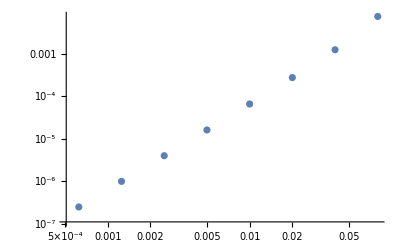

```mathematica
ListLogLogPlot[Table[{listspar[[i]],Abs[1-modesOldpex[[i]]["ω"]/modesNewpex[[i]]["ω"]]},{i,1,Length[listspar]}]]
```

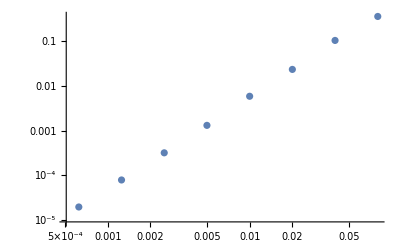

```mathematica
ListLogLogPlot[Table[{listspar[[i]],Abs[1-modesOldpex[[i]]["Amplitudes"]["ℐ"]/modesNewpex[[i]]["Amplitudes"]["ℐ"]]},{i,1,Length[listspar]}]]
```

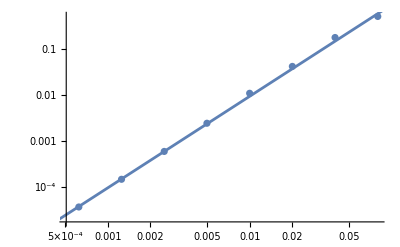

```mathematica
Show[ListLogLogPlot[Table[{listspar[[i]],Abs[1-modesOldpex[[i]]["Fluxes"]["Energy"]["ℐ"]/modespex[[i]]["Fluxes"]["Energy"]["ℐ"]]},{i,1,Length[listspar]}]],LogLogPlot[(spar/2.5*^-3)^2*5.91*^-4,{spar,0.0001,0.1}]]
```

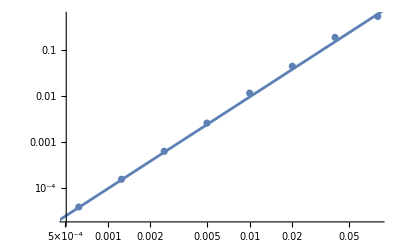

```mathematica
Show[ListLogLogPlot[Table[{listspar[[i]],Abs[1-modesOldpex[[i]]["Fluxes"]["Energy"]["ℐ"]/modesNewpex[[i]]["Fluxes"]["Energy"]["ℐ"]]},{i,1,Length[listspar]}]],LogLogPlot[(spar/2.5*^-3)^2*5.91*^-4,{spar,0.0001,0.1}]]
```

## Trajectory

```mathematica
spar=0.01`64
```

0.01

```mathematica
orbit=KerrSpinOrbit[a,p,e,x,spar];
```

```mathematica
orbit["EnTilde"]
```

0.96193206532501987761035387678814113600255217793762678028932177

```mathematica
orbit["TrajectoryDeltas"]["Δtr"][0.3`48]
```

-5.5001189855621301979833054228455586711238547

```mathematica
orbit["Trajectoryg"][[1]][0.1,0.2,0.3]
```

-3.57508

```mathematica
orbit["Trajectoryg"][[4]][2Pi,0.2,0.3]
```

6.35421

```mathematica
orbit["δx"][0.2,0.3]
```

{0.040103,2.96701,0.00407446,0.00202126}

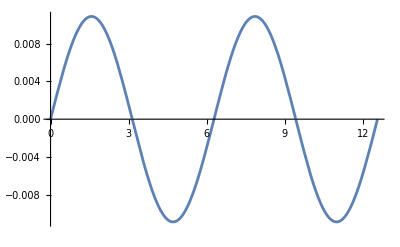

```mathematica
Plot[orbit["TrajectoryDeltas"]["Δϕr"][qr],{qr,0,4Pi}]
```

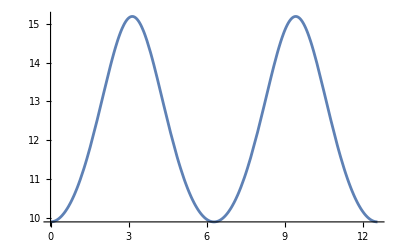

```mathematica
Plot[orbit["Trajectoryg"][[2]][qr],{qr,0,4Pi}]
```

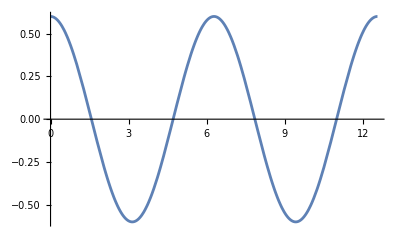

```mathematica
Plot[orbit["Trajectoryg"][[3]][qz],{qz,0,4Pi}]
```

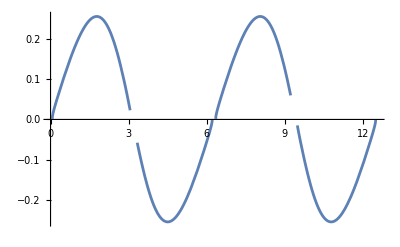

```mathematica
Plot[orbit["δx"][qr,0.3][[1]],{qr,0,4Pi}]
```

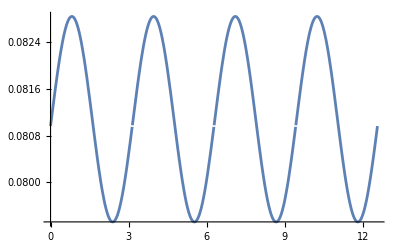

```mathematica
Plot[orbit["δx"][0.4,qz][[1]],{qz,0,4Pi}]
```

```mathematica
Plot3D[orbit["δx"][qr,qz][[2]],{qr,0,4Pi},{qz,0,4Pi}]
```

-Graphics3D-

```mathematica
Plot3D[orbit["δx"][qr,qz][[3]],{qr,0,4Pi},{qz,0,4Pi}]
```

-Graphics3D-

```mathematica
Plot3D[orbit["δx"][qr,qz][[4]],{qr,0,4Pi},{qz,0,4Pi}]
```

-Graphics3D-